# Prices plot

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"],Orange,Purple,Brown};
```

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_DAX_MXX_NIKKEI_dataset.wdx"}];
database = Import[path];
```

```mathematica
ipc = database[[3]];
```

## Prices

```mathematica
ipc // Keys
```

{Name,Dates,Prices,DatedPrices,Returns,TrendReturns,VelocityTrendReturns,DatedReturns,DatedTrendReturns,DatedVelocityTrendReturns}

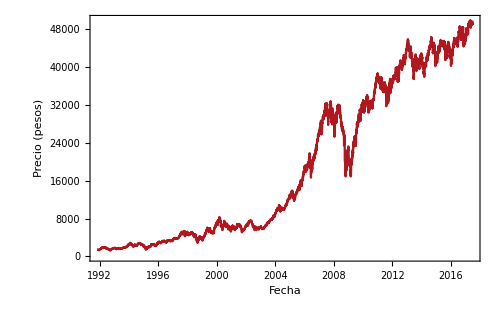

```mathematica
DateListPlot[
ipc["DatedPrices"],
PlotRange->All,
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Fecha",15],Style["Precio (pesos)",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->First[colors],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
```